James Gardner
Working from Yap thesis, 2020
Deriving eq. 7.12 from eq. 7.8 and eq. 7.17 from 7.16.

Watch out, Yap thesis uses X_2=-i(a+a†) which gives a different sign in the 2nd and 4th rows of Γ

```mathematica
(*I is reserved for ⅈ, be careful not to confuse I and Id!*)
Id=IdentityMatrix[4];
(*eq. 7.6*)
M=κa({{-1, 0, 0, x ⅇ^(ⅈ θb)}, {0, -1, x ⅇ^(-ⅈ θb), 0}, {0, x ⅇ^(ⅈ θb), -1, 0}, {x ⅇ^(-ⅈ θb), 0, 0, -1}});
(*eq 7.11*)
Γ=({{1, 1, 0, 0}, {-ⅈ, ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, -ⅈ, ⅈ}});
Xfin=({{Xfins1}, {Xfins2}, {Xfini1}, {Xfini2}});
Xlin=({{Xlins1}, {Xlins2}, {Xlini1}, {Xlini2}});
```

```mathematica
(*eqs. 7.9, 7.10*)
T =FullSimplify[2κaf Γ.Inverse[ⅈ ω Id-M].Inverse[Γ]-Id];
Tl = FullSimplify[2(κaf κal)^(1/2)Γ. Inverse[ⅈ ω Id-M].Inverse[Γ]];
```

```mathematica
Xfout=FullSimplify[T.Xfin+Tl.Xlin];
Xfout//MatrixForm
```

(-(2 Xlins1 √(κaf κal) (κa+ⅈ ω)+Xfins1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)+2 x κa ((Xfini1 κaf+Xlini1 √(κaf κal)) Cos[θb]+(Xfini2 κaf+Xlini2 √(κaf κal)) Sin[θb]))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlins2 √(κaf κal) (κa+ⅈ ω)+Xfins2 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)-2 x κa (Xfini2 κaf+Xlini2 √(κaf κal)) Cos[θb]+2 x κa (Xfini1 κaf+Xlini1 √(κaf κal)) Sin[θb])/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlini1 √(κaf κal) (κa+ⅈ ω)+Xfini1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)+2 x κa ((Xfins1 κaf+Xlins1 √(κaf κal)) Cos[θb]+(Xfins2 κaf+Xlins2 √(κaf κal)) Sin[θb]))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlini2 √(κaf κal) (κa+ⅈ ω)+Xfini2 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)-2 x κa (Xfins2 κaf+Xlins2 √(κaf κal)) Cos[θb]+2 x κa (Xfins1 κaf+Xlins1 √(κaf κal)) Sin[θb])/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2))

```mathematica
Collect[Xfout[[1]][[1]]/.{θb->0},{Xlins1,Xlins2,Xlini1,Xlini2,Xfins1,Xfins2,Xfini1,Xfini2}]
```

-(2 x Xfini1 κa κaf)/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(2 x Xlini1 κa √(κaf κal))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(2 Xlins1 √(κaf κal) (κa+ⅈ ω))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(Xfins1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)

```mathematica
(*the variance of Xfouts1: if assuming all inputs are vacuum, then just sum the abs sq of the co-efficients of each input fluctuation.*)
Vout=FullSimplify[(1/(((-1+x^2) κa^2+ω^2)^2+(-2  κa ω)^2))((-2 x κa κaf)^2+ (-2 x κa √(κaf κal))^2+(-2 κa√(κaf κal))^2+(-2 √(κaf κal)ω)^2+(κa ((-1+x^2) κa+2 κaf)+ω^2)^2+(-2 (κa-κaf) ω)^2)/.{κal->κa-κaf}]
```

1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)

```mathematica
(*if the idler doesn't recieve input from f-port, then turn off Xfini1,Xfini2=0*)
VnoIdlerIn=FullSimplify[(1/(((-1+x^2) κa^2+ω^2)^2+(-2  κa ω)^2))( (-2 x κa √(κaf κal))^2+(-2 κa√(κaf κal))^2+(-2 √(κaf κal)ω)^2+(κa ((-1+x^2) κa+2 κaf)+ω^2)^2+(-2 (κa-κaf) ω)^2)/.{κal->κa-κaf}]
Simplify[VnoIdlerIn==1+(4 x^2 κa^2 κaf(2κa-κaf))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)]
```

(((1+x)^2 κa^2-2 x κa κaf+ω^2) ((-1+x)^2 κa^2+2 x κa κaf+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)

True

```mathematica
(*for reference, the desired value is (7.12, 7.18)*)
Goal=Simplify[1+(8 x^2(κaf/κa))/(x^4+2 x^2((ω/κa)^2-1)+((ω/κa)^2+1)^2)];
Goal==Vout
```

True

```mathematica
(*Attempting to recover 7.17, the covariance matrix*)
Assumps = {x>0,κa>0,κaf>0,κal>0,θb>0,ω>0,κa≥κaf};
V = FullSimplify[(T.ConjugateTranspose[T]+Tl.ConjugateTranspose[Tl])/.{κal->κa-κaf},Assumptions->Assumps];
V//MatrixForm
```

(1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | (4 x κa κaf ((1+x^2) κa^2+ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | (4 x κa κaf ((1+x^2) κa^2+ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)
0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | (4 x κa κaf ((1+x^2) κa^2+ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | -(4 x κa κaf ((1+x^2) κa^2+ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)
(4 x κa κaf ((1+x^2) κa^2+ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | (4 x κa κaf ((1+x^2) κa^2+ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0
(4 x κa κaf ((1+x^2) κa^2+ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | -(4 x κa κaf ((1+x^2) κa^2+ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4))

```mathematica
V[[1]][[1]]
```

1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)

```mathematica
(*the diagonal elements of the covariance matrix are the output variances*)
V[[1]][[1]] == Vout==Goal
```

True

Repeating calculation using other convention for Γ

```mathematica
Γsgn=({{1, 1, 0, 0}, {ⅈ, -ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, ⅈ, -ⅈ}});
Tfsgn =FullSimplify[2κaf Γsgn.Inverse[ⅈ Ω Id-M].Inverse[Γsgn]-Id];
Tlsgn = FullSimplify[2(κaf κal)^(1/2)Γsgn. Inverse[ⅈ Ω Id-M].Inverse[Γsgn]];
Vsgn=FullSimplify[(Tfsgn.Tfsgn†+Tlsgn.Tlsgn†)/.{κal->κa-κaf},Assumptions->{x>0,θb>0,κaf>0,Ω>0,κa≥κaf}];
Vsgn//MatrixForm
(*opposite convention flips the sign of θb*)
(V/.{ω->Ω,θb->-θb})==Vsgn
```

(1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | (4 x κa κaf ((1+x^2) κa^2+Ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | -(4 x κa κaf ((1+x^2) κa^2+Ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4)
0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | -(4 x κa κaf ((1+x^2) κa^2+Ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | -(4 x κa κaf ((1+x^2) κa^2+Ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4)
(4 x κa κaf ((1+x^2) κa^2+Ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | -(4 x κa κaf ((1+x^2) κa^2+Ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0
-(4 x κa κaf ((1+x^2) κa^2+Ω^2) Sin[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | -(4 x κa κaf ((1+x^2) κa^2+Ω^2) Cos[θb])/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4))

True

```mathematica
SetDirectory[NotebookDirectory[]];
(*print the notebook to a .pdf, the notebook needs to be saved for this to function*)
NotebookPrint[EvaluationNotebook[],NotebookDirectory[]<>"NOPO_matrices.pdf"]
```

Plotting the (co)variances from degenerate and nondegenerate OPO’s against frequency

```mathematica
-Graphics-;
```

```mathematica
(*above: eq3.5 from Min Jet's thesis, the κ formula is only an approximation?*)
```

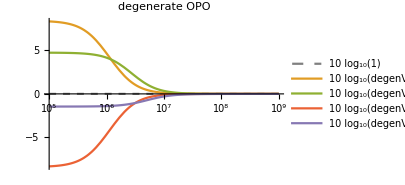
-Graphics-frequency, f=Ω/(2  π) / (log scale)variance / dB (10log_10)

```mathematica
(*degenerate OPO, using values from Sheon Chua's thesis*)
c=3 10^8(*m s^-1*);
L =1(*m*);
tRoundTrip=(2L)/c(*=1/FSR*); (*assumes linear cavity, unclear if factor of 2 req*)
Tout=0.1;
kout=-1/(2 tRoundTrip)Log[1-Tout];
x=0.45;
degenV1[w_,Tin_,Tloss_]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
1+(4 kout g)/(w^2+(g-ktot)^2))
degenV2[w_,Tin_,Tloss_]:=((*just send g->-g*)
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
1-(4 kout g)/(w^2+(g+ktot)^2))
(*(*λ=1μm=10^-6 m, want to consider sidebands of carrier, so look at frequencies around w=2π c/λ*)
(*because of rotating frame, aren't all frequencies already relative to ω/2?*)
lambda=10^-6(*m*);
wCarrier=N[2π c/lambda];(*~1.9*10^15 Hz*)*)
(*Labeled[LogLogPlot[{1,degenV1[w,Tin=0,Tloss=0],degenV1[w,Tin=0.01,Tloss=0.1],degenV2[w,Tin=0,Tloss=0],degenV2[w,Tin=0.01,Tloss=0.1]},{w,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"degenerate OPO",PlotStyle->{{Dashed,Gray},,,,},ImageSize->300],{"angular frequency / (log scale)", "variance / (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
(*plotting quantum noise in dB is a matter of: (1) understanding what kind of quantity you are plotting and (2) plotting relative to vacuum,
e.g.1 for variance which is a squared (power) quantity, plot 10 Subscript[log, 10](V=σ^2) since vacuum is 1,
e.g.2 for shot noise transfer fn, |R| is amplitude,  plot 20 Subscript[log, 10](|R|) since |R|_vac is 1*)
Labeled[LogLinearPlot[{
10Log10[1],
10Log10[degenV1[2π f,Tin=0,Tloss=0]],
10Log10[degenV1[2π f,Tin=0.1,Tloss=0.1]],
10Log10[degenV2[2π f,Tin=0,Tloss=0]],
10Log10[degenV2[2π f,Tin=0.1,Tloss=0.1]]},{f,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"degenerate OPO",PlotStyle->{{Dashed,Gray},,,,},ImageSize->300,PlotRange->All],{"frequency, f=Ω/(2  π) / (log scale)", "variance / dB (10log_10)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

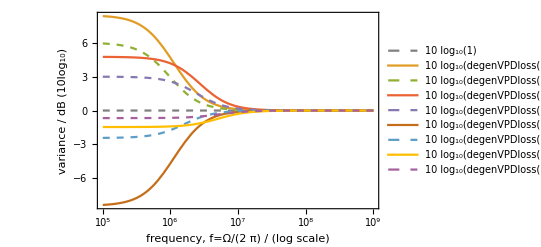

```mathematica
(*introducing PD loss as well, Subscript[R, PD] is the reflectivity of the lossless beam-splitter between (trans) and (PD) fields*)
x=0.45;
degenVPDloss[Ω_,Tin_,Tloss_,Rpd_,gsgn_:1]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=gsgn x ktot;
1+(4 kout g(1-Rpd))/(Ω^2+(g-ktot)^2))
LogLinearPlot[{
10Log10[1],
10Log10[degenVPDloss[2π f,Tin=0,Tloss=0,Rpd=0,gsgn=1]],
10Log10[degenVPDloss[2π f,Tin=0,Tloss=0,Rpd=0.5,gsgn=1]],
10Log10[degenVPDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0,gsgn=1]],
10Log10[degenVPDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0.5,gsgn=1]],10Log10[degenVPDloss[2π f,Tin=0,Tloss=0,Rpd=0,gsgn=-1]],
10Log10[degenVPDloss[2π f,Tin=0,Tloss=0,Rpd=0.5,gsgn=-1]],
10Log10[degenVPDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0,gsgn=-1]],
10Log10[degenVPDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0.5,gsgn=-1]]},{f,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotStyle->{{Dashed,Gray},,Dashed,,Dashed,,Dashed,,Dashed},ImageSize->400,PlotRange->All,Frame->True,FrameLabel->{{ "variance / dB (10log_10)",},{"frequency, f=Ω/(2  π) / (log scale)",StringForm["degenerate OPO\nintracavity and PD loss\nsqueezing param. x=``",x]}}]
```

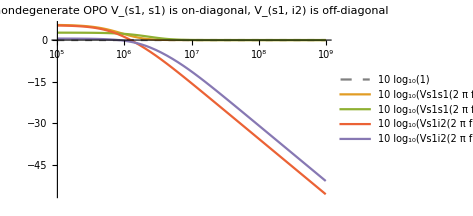
-Graphics-frequency, f=Ω/(2  π) / (log scale)covariance / dB (10log_10)

```mathematica
(*nondegenerate OPO, from above calculation: V[[1]][[1]], V[[1]][[3]]*)
Vs1s1[w_,Tin_,Tloss_]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
1+(8 x^2 ktot^3 kout)/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
Vs1i2[w_,Tin_,Tloss_]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
(4 x ktot kout ((1+x^2) ktot^2+w^2))/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
Labeled[LogLinearPlot[{
10Log10[1],
10Log10[Vs1s1[2π f,Tin=0,Tloss=0]],
10Log10[Vs1s1[2π f,Tin=0.1,Tloss=0.1]],
10Log10[Vs1i2[2π f,Tin=0,Tloss=0]],
10Log10[Vs1i2[2π f,Tin=0.1,Tloss=0.1]]},{f,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"nondegenerate OPO\nV_(s1, s1) is on-diagonal, V_(s1, i2) is off-diagonal",PlotStyle->{{Dashed,Gray},,,,},ImageSize->350],{"frequency, f=Ω/(2  π) / (log scale)", "covariance / dB (10log_10)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

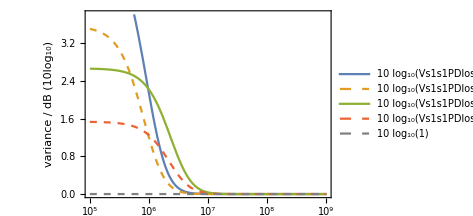
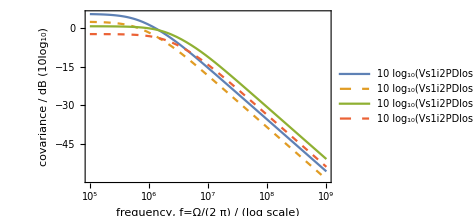

```mathematica
(*adding PD loss, see degenerate OPO case for description of Rpd*)
Vs1s1PDloss[w_,Tin_,Tloss_,Rpd_]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
1+(8 x^2 ktot^3 kout(1-Rpd))/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
Vs1i2PDloss[w_,Tin_,Tloss_,Rpd_]:=(
kin=-1/(2 tRoundTrip)Log[1-Tin];
kloss=-1/(2 tRoundTrip)Log[1-Tloss];
ktot=kout+kin+kloss;
g=x ktot;
(4 x ktot kout ((1+x^2) ktot^2+w^2)(1-Rpd))/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
(*plotting*)
p1=LogLinearPlot[{
10Log10[Vs1s1PDloss[2π f,Tin=0,Tloss=0,Rpd=0]],
10Log10[Vs1s1PDloss[2π f,Tin=0,Tloss=0,Rpd=0.5]],
10Log10[Vs1s1PDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0]],
10Log10[Vs1s1PDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0.5]],
10Log10[1]},{f,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotStyle->{,Dashed,,Dashed,{Dashed,Gray}},ImageSize->350,Frame->True,FrameLabel->{{"variance / dB (10log_10)",},{,"nondegenerate OPO\nV_(s1, s1) on-diagonal (top), V_(s1, i2) off-diagonal terms (bottom)\nPD and intracavity loss"}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},ImagePadding->{{40,1},{1,60}},PlotRange->All];
p2=LogLinearPlot[{
10Log10[Vs1i2PDloss[2π f,Tin=0,Tloss=0,Rpd=0]],
10Log10[Vs1i2PDloss[2π f,Tin=0,Tloss=0,Rpd=0.5]],
10Log10[Vs1i2PDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0]],
10Log10[Vs1i2PDloss[2π f,Tin=0.1,Tloss=0.1,Rpd=0.5]]},{f,10^5,10^9},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],ImageSize->350,Frame->True,PlotStyle->{,Dashed}, FrameLabel->{{"covariance / dB (10log_10)",},{"frequency, f=Ω/(2  π) / (log scale)",}},ImagePadding->{{40,1},{50,1}}];
Column[{p1,p2},Spacings->0]
```

```mathematica
(*demonstrating squeezing, linear combinations of quadratures*)
Clear[x]
(*watch out for re-normalisation of combined quadrature, here 2^(-1/2) has been taken*)
Vcom[ψ_,Rpd_]:=1+(1-Rpd)((4 x κa κaf (2 x κa^2 +Sin[2ψ]((1+x^2) κa^2+ω^2)))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4))
2Vcom[π/4,0]
(*need to show for degenerate OPO that θb≠0 results are given by a linear combination of θb=0 quadratures*)
Clear[g]
Idd=IdentityMatrix[2];
Γd=({{1, 1}, {-I, I}});
Md=({{0, Exp[I θb]}, {Exp[-I θb], 0}});
Asumpsd={κaf>0,κa>κaf,g>0,Ω>0,Element[θb,Reals]};
Td=Simplify[2 κaf Γd.Inverse[(κa-I Ω)Idd-g Md].Inverse[Γd]-Idd,Assumptions->Asumpsd];
Rd=Simplify[2 (κaf(κa-κaf))^(1/2) Γd.Inverse[(κa-I Ω)Idd-g Md].Inverse[Γd],Assumptions->Asumpsd];
Vd=FullSimplify[Td.ConjugateTranspose[Td]+Rd.ConjugateTranspose[Rd],Assumptions->Asumpsd];
Vd//MatrixForm
FullSimplify[Vd/.{θb->0}]//MatrixForm
Simplify[((Vd[[1]][[1]])/.{g->x κa})==1+(4 x κa κaf (2 x κa^2 +Cos[θb]((1+x^2) κa^2+Ω^2)))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4)]
(*to-do: check this covariance matrix - rows are Subscript[X̂, 1] and Subscript[X̂, 2], surely covariances should be zero for degenerate OPO given vacuum inputs?*)
```

2 (1+(4 x κa κaf (2 x κa^2+(1+x^2) κa^2+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4))

((g^4+(κa^2+Ω^2)^2+2 g^2 (-κa^2+4 κa κaf+Ω^2)+4 g κaf (g^2+κa^2+Ω^2) Cos[θb])/(((g-κa)^2+Ω^2) ((g+κa)^2+Ω^2)) | (4 g κaf (g^2+κa^2+Ω^2) Sin[θb])/(((g-κa)^2+Ω^2) ((g+κa)^2+Ω^2))
(4 g κaf (g^2+κa^2+Ω^2) Sin[θb])/(g^4+2 g^2 (-κa^2+Ω^2)+(κa^2+Ω^2)^2) | (g^4+(κa^2+Ω^2)^2+2 g^2 (-κa^2+4 κa κaf+Ω^2)-4 g κaf (g^2+κa^2+Ω^2) Cos[θb])/(((g-κa)^2+Ω^2) ((g+κa)^2+Ω^2)))

(1+(4 g κaf)/((g-κa)^2+Ω^2) | 0
0 | 1-(4 g κaf)/((g+κa)^2+Ω^2))

True